Assignment 3
ELEC-E7460 Modeling and Simulation, fall 2018
Adam Ilyas 725819

```mathematica
Needs["HypothesisTesting`"]
```

Question 1a) Dispatching problem

 Your first task is to create a simulator for the dispatching problem as discussed in the
lecture. 

New jobs arrive to the system according to a Poisson process with rate λ. 

There are two parallel queues with rates μ 1 and μ 2 having infinite buffers for the jobs. The service
times in both queues are independent and exponentially distributed. Jobs in the queue are
processed according to the FIFO discipline. 

As statistics, collect the delays of the jobs and in particular the overall mean delay of the jobs.

```mathematica
loadBalanceSimulator[la_, mu1_, mu2_, iniTrans_, simuLen_, policy_] := 
Module[
{simTime, prevEvTime, nextArr, nextDep,
joblist1, joblist2, 
delsum1, delsum2,
nofsamples1,nofsamples2,
depInd,deptime1,deptime2,i},

(* Initialize to zero *)
simTime=0;
delsum1=0;
delsum2=0;
nofsamples1= 0;
nofsamples2=0;

(* Initialize *)
nextArr=RandomVariate[ExponentialDistribution[la]];
nextDep=Infinity;

(* Initialize empty joblist *)
joblist1={};
joblist2={};

While[simTime ≤ simuLen,
If[nextArr < nextDep,
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextArr; (* move time to new event *)
(* serves flow *)
If[Length[joblist1]>0,joblist1[[1,2]]-=(simTime-prevEvTime)];
If[Length[joblist2]>0,joblist2[[1,2]]-=(simTime-prevEvTime)];

(* insert new arrival based on policy *)
Which[
policy== "rand",
(* Randomized load balancing policy:
In this policy,-an arriving job is routed to queue 1 with probability μ1/(μ1+μ2)
otherwise to queue 2 *)
{
If[RandomReal[]<mu1/(mu1+mu2), 
{joblist1=Append[joblist1,{simTime,RandomVariate[ExponentialDistribution[mu1]]}]},
(* else if p > mu1/(mu1 + mu2)*)
{joblist2=Append[joblist2,{simTime,RandomVariate[ExponentialDistribution[mu2]]}]}
(* end if *)];
},
policy== "jsq",
(*  JSQ (Join-the-Shortest-Queue):
Route the arrival to the queue with smallest number of jobs. 
In case of a tie,choose the queue randomly.*)
{
(* insert new arrival *)
Which[
Length[joblist1] < Length[joblist2],
joblist1=Append[joblist1,{simTime,RandomVariate[ExponentialDistribution[mu1]]}],
Length[joblist1] > Length[joblist2],
joblist2=Append[joblist2,{simTime,RandomVariate[ExponentialDistribution[mu2]]}],
Length[joblist1]==Length[joblist2],
{If[RandomReal[]<0.5,
joblist1=Append[joblist1,{simTime,RandomVariate[ExponentialDistribution[mu1]]}],
joblist2=Append[joblist2,{simTime,RandomVariate[ExponentialDistribution[mu2]]}]
];}
];
},
policy== "wjsq",
(* Weighted-Join Shortest Queue:
Route the arrival to the queue i with the smallestSubscript[x, i]/Subscript[μ, i] ,i={1,2},where x is the number of jobs in queue i.
Again,in case of a tie,choose the queue randomly.*)
{
(* insert new arrival *)
Which[
Length[joblist1]/mu1 < Length[joblist2]/mu2,
joblist1=Append[joblist1,{simTime,RandomVariate[ExponentialDistribution[mu1]]}],
Length[joblist1]/mu1 > Length[joblist2]/mu2,
joblist2=Append[joblist2,{simTime,RandomVariate[ExponentialDistribution[mu2]]}],
Length[joblist1]/mu1==Length[joblist2]/mu2,
{If[RandomReal[]<0.5,
joblist1=Append[joblist1,{simTime,RandomVariate[ExponentialDistribution[mu1]]}],
joblist2=Append[joblist2,{simTime,RandomVariate[ExponentialDistribution[mu2]]}]
];}
];
}
];
(* update arrival event *)
nextArr=simTime+RandomVariate[ExponentialDistribution[la]];
(* update departure event, there is at least 1 flow in system *)
If[Length[joblist1]>0,deptime1=simTime+joblist1[[1,2]],deptime1=Infinity];
If[Length[joblist2]>0,deptime2=simTime+joblist2[[1,2]],deptime2=Infinity];
If[deptime1<deptime2,
{nextDep=deptime1; depInd=1;},
{nextDep=deptime2; depInd=2;}];
}, 
(* else if nextArr ≥ nextDep *)
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextDep; (* move time to new event *)
(* serve flows *)
If[Length[joblist1]>0,joblist1[[1,2]]-=(simTime-prevEvTime)];
If[Length[joblist2]>0,joblist2[[1,2]]-=(simTime-prevEvTime)];
(* collect statistics *)
Which[
depInd==1,
{If[simTime>iniTrans,
{delsum1+=(simTime-joblist1[[1,1]]);
nofsamples1++}];
joblist1=Delete[joblist1,1];},
depInd == 2,
{If[simTime>iniTrans,
{delsum2+=(simTime-joblist2[[1,1]]);
nofsamples2++}];
joblist2=Delete[joblist2,1];}
];
(* update departure event, now system may be totally empty *)
If[Length[joblist1]>0,deptime1=simTime+joblist1[[1,2]],deptime1=Infinity];
If[Length[joblist2]>0,deptime2=simTime+joblist2[[1,2]],deptime2=Infinity];
If[(Length[joblist1]+Length[joblist2])>0,
{If[deptime1<deptime2,
{nextDep=deptime1;
depInd=1},
{nextDep=deptime2;
depInd=2}];
},
{nextDep=Infinity;}
];
}
(* end if *)]
(* end while *)];

(* Return mean delay of jobs: 
total delay/ total no of samples *)
(delsum1 + delsum2) / (nofsamples1 + nofsamples2)
]
```

1a)
Check that your simulator is working properly with the following parameters: 
λ = 1.8,
 μ 1 =1,
  μ 2 = 2

```mathematica
la=1.8;mu1=1;mu2=2;
meanDelay1 = loadBalanceSimulator[la,mu1,mu2,10000,150000, "rand"];
meanDelay2 = loadBalanceSimulator[la,mu1,mu2,10000,150000, "jsq"];
meanDelay3 = loadBalanceSimulator[la,mu1,mu2,10000,150000, "wjsq"];
```

```mathematica
Print[StringForm["Randomized load balancing: overall mean delay `` time units", 
NumberForm[meanDelay1, 3]]];
Print[StringForm["Join Shortest Queue: overall mean delay `` time units", 
NumberForm[meanDelay2, 3]]];
Print[StringForm["Weighted Join Shortest Queue: overall mean delay `` time units", 
NumberForm[meanDelay3, 3]]];
```

Randomized load balancing: overall mean delay 1.66 time units

Join Shortest Queue: overall mean delay 1.21 time units

Weighted Join Shortest Queue: overall mean delay 1.14 time units

1b)
Consider now the system with the following service rates μ 1 = 1 and μ 2 = 4. Thus,
the system is stable if λ < 5. 

Simulate the system with the following load values 
ρ ={0.1, 0.3, 0.5, 0.6, 0.7, 0.8}.

 Recall that load ρ = λ/(μ 1 + μ 2 ). Estimate 
 the overall mean delay of the jobs for the different policies (randomized load balancing, JSQ, WJSQ) and 
 the corresponding 95% confidence intervals.

```mathematica
mu1=1;
mu2=4;
loads = {0.1,0.3,0.5,0.6,0.7,0.8};
policies = {"rand", "jsq", "wjsq"};
```

```mathematica
resultsTable = {{},{},{}};

For[i=1,i≤Length[policies],i++,
(* Different policy *)
policy = policies[[i]];
Print[StringForm["Policy: ``", policy]];

For[j=1,j≤Length[loads],j++,
p = loads[[j]];
la = p*(mu1+mu2); (* lambda *)
results = Table[loadBalanceSimulator[la, mu1, mu2, 10000,150000, policy],{10}];
mean = Mean[results];
ci = MeanCI[results];
resultsTable[[i]] = Append[resultsTable[[i]],mean ];
Print[StringForm["When load: ``, Mean: ``, 95% Confidence Interval = ``",
p,NumberForm[mean, 5], ci]];
];
];
```

Policy: rand

When load: 0.1, Mean: 0.4443, 95% Confidence Interval = {0.441161,0.447445}

When load: 0.3, Mean: 0.56986, 95% Confidence Interval = {0.567934,0.571783}

When load: 0.5, Mean: 0.7982, 95% Confidence Interval = {0.794924,0.801467}

When load: 0.6, Mean: 1.0021, 95% Confidence Interval = {0.996013,1.00817}

When load: 0.7, Mean: 1.3288, 95% Confidence Interval = {1.32323,1.33443}

When load: 0.8, Mean: 1.9894, 95% Confidence Interval = {1.96546,2.01337}

Policy: jsq

When load: 0.1, Mean: 0.58661, 95% Confidence Interval = {0.584228,0.589001}

When load: 0.3, Mean: 0.6192, 95% Confidence Interval = {0.617762,0.620643}

When load: 0.5, Mean: 0.75729, 95% Confidence Interval = {0.755513,0.759059}

When load: 0.6, Mean: 0.88313, 95% Confidence Interval = {0.878981,0.887284}

When load: 0.7, Mean: 1.0843, 95% Confidence Interval = {1.08088,1.08768}

When load: 0.8, Mean: 1.4735, 95% Confidence Interval = {1.46413,1.48292}

Policy: wjsq

When load: 0.1, Mean: 0.57069, 95% Confidence Interval = {0.568746,0.572625}

When load: 0.3, Mean: 0.54304, 95% Confidence Interval = {0.542137,0.543945}

When load: 0.5, Mean: 0.61113, 95% Confidence Interval = {0.609361,0.612903}

When load: 0.6, Mean: 0.70014, 95% Confidence Interval = {0.698524,0.701751}

When load: 0.7, Mean: 0.85885, 95% Confidence Interval = {0.854486,0.863224}

When load: 0.8, Mean: 1.1945, 95% Confidence Interval = {1.18841,1.20059}

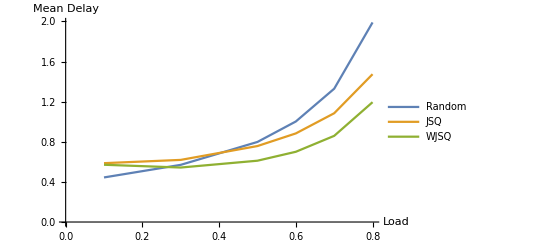

```mathematica
data1 = Transpose@{loads, resultsTable[[1]]};
data2 = Transpose@{loads, resultsTable[[2]]};
data3 = Transpose@{loads, resultsTable[[3]]};
ListLinePlot[{Legended[data1, "Random"], Legended[data2, "JSQ"], Legended[data3, "WJSQ"]}, AxesLabel-> {"Load", "Mean Delay"}]
```